## Gate Transformation

-Graphics-

```mathematica
B[t_]={{t,ⅈ √(1-t^2)},{ⅈ  √(1-t^2),t}};
Subscript[t, 1]=√(2/3);
Subscript[t, 2]=(√3)/2;
Subscript[t, 3]=1/(√2);
```

## Modes T and a mix at the first beam splitter:

```mathematica
{Subscript[c, T],Subscript[c, a]}=B[Subscript[t, 1]].{Subscript[c, T1],Subscript[c, a1]};
```

## Nonlinear phase gate

```mathematica
(*{Subscript[A, 0],Subscript[A, 1],Subscript[A, 2]}=CoefficientList[Expand[ψ],Subscript[c, T1]];
ψ=Subscript[A, 0]+Subscript[A, 1] Subscript[c, T1]+ⅇ^(ⅈ X)Subscript[A, 2] Subscript[c, T1]^2;*)
```

```mathematica
BNSG[θ_,ϕ_]:={{Cos[θ],-ⅇ^(+ⅈ ϕ)Sin[θ]},{+ⅇ^(-ⅈ ϕ)Sin[θ],Cos[θ]}};
θ1=π/8; ϕ1=0;
θ2=65.5302/180 π; ϕ2=0;
θ3=-π/8; ϕ3=0;
ϕ4=π;
```

#### after Beam splitter 1 ( coupling modes 2 and 3)

```mathematica
{Subscript[c, 21],Subscript[c, 31]}=BNSG[θ1,ϕ1].{Subscript[c, 22],Subscript[c, 32]};
Subscript[c, T1]=ⅇ^(-ⅈ ϕ4)Subscript[c, T2];
```

#### after Beam splitter 2 (coupling modes 1 and 2)

```mathematica
{Subscript[c, T2],Subscript[c, 22]}=BNSG[θ2,ϕ2].{Subscript[c, T3],Subscript[c, 23]};
Subscript[c, 32]=Subscript[c, 33];
```

#### after Beam splitter 3 (coupling modes 2 and 3)

```mathematica
{Subscript[c, 23],Subscript[c, 33]}=BNSG[θ3,ϕ3].{Subscript[c, 24],Subscript[c, 34]};
Subscript[c, T3]=Subscript[c, T4];
```

#### Inefficient detectors

```mathematica
{Subscript[c, 24],Subscript[c, 2vac]}=B[√η].{Subscript[c, 25],Subscript[c, 2d]};
{Subscript[c, 34],Subscript[c, 3vac]}=B[√η].{Subscript[c, 35],Subscript[c, 3d]};
Subscript[c, T4]=Subscript[c, T5];
```

## Modes T1 and b mix at the second beam splitter:

```mathematica
{Subscript[c, T5],Subscript[c, b]}=B[Subscript[t, 2]].{Subscript[c, T6],Subscript[c, b1]};
```

## Modes T2 and c mix at the third beam splitter:

```mathematica
{Subscript[c, T6],Subscript[c, c]}=B[Subscript[t, 3]].{Subscript[c, T7],Subscript[c, c1]};
```

## Inefficient detectors: Modelled as Perfect ones with beam splitter of t=√η

```mathematica
{Subscript[c, a1],Subscript[c, ad1]}=B[√η].{Subscript[c, ap],Subscript[c, ad]};
{Subscript[c, b1],Subscript[c, bd1]}=B[√η].{Subscript[c, bp],Subscript[c, bd]};
{Subscript[c, c1],Subscript[c, cd1]}=B[√η].{Subscript[c, cp],Subscript[c, cd]};
```

## Results

```mathematica
Subscript[ψ, T]=α +β Subscript[c, T];
Subscript[ψ, CA]=γ Subscript[c, b]+δ Subscript[c, a];(*γ01+δ10*)
ψ=Expand[Subscript[ψ, T] Subscript[ψ, CA] Subscript[c, 21]];
creationops=FullSimplify[CoefficientList[CoefficientList[ψ,{Subscript[c, ap],Subscript[c, bp],Subscript[c, cp],Subscript[c, 25],Subscript[c, 35]}][[1,1,2,2,1]],{Subscript[c, 2d],Subscript[c, 3d],Subscript[c, ad],Subscript[c, bd],Subscript[c, cd],Subscript[c, T7]},{3,3,3,3,3,3}]];
fockstate=Table[√((i-1)!(j-1)!(k-1)!(l-1)!(m-1)!(n-1)!)creationops[[i,j,k,l,m,n]],{i,1,3},{j,1,3},{k,1,3},{l,1,3},{m,1,3},{n,1,3}];

P=Map[Abs[#]^2&,fockstate,{6}];
```

## Fidelity

```mathematica
F[η_,α_,γ_,ϕT_,ϕC_]=Module[{},
β=√(1-α^2)ⅇ^(ⅈ ϕT);
δ=√(1-γ^2)ⅇ^(ⅈ ϕC);
Total[P[[1,1,1,1,1]]]/Total[P,6]
];
AvF[η_]:=N[1/(2π)^2 NIntegrate[F[η,α,γ,ϕT,ϕC],{α,0,1},{γ,0,1},{ϕT,0,2π},{ϕC,0,2π}]];
```

## C-Phase with KLM

## after 50-50 Beam splitter on the left

```mathematica
{t10,b10}=BNSG[π/4,0].{t11,b11};
```

## Top

#### after Beam splitter 1 ( coupling modes 2 and 3)

```mathematica
{t21,t31}=BNSG[θ1,ϕ1].{t22,t32};
t11=ⅇ^(-ⅈ ϕ4)t12;
```

#### after Beam splitter 2 (coupling modes 1 and 2)

```mathematica
{t12,t22}=BNSG[θ2,ϕ2].{t13,t23};
t32=t33;
```

#### after Beam splitter 3 (coupling modes 2 and 3)

```mathematica
{t23,t33}=BNSG[θ3,ϕ3].{t24,t34};
t13=t14;
```

#### Inefficient detectors

```mathematica
{t24,t2vac}=B[√η].{t25,t2dump};
{t34,t3vac}=B[√η].{t35,t3dump};
t14=t15;
```

## Bottom

#### after Beam splitter 1 ( coupling modes 2 and 3)

```mathematica
{b21,b31}=BNSG[θ1,ϕ1].{b22,b32};
b11=ⅇ^(-ⅈ ϕ4)b12;
```

#### after Beam splitter 2 (coupling modes 1 and 2)

```mathematica
{b12,b22}=BNSG[θ2,ϕ2].{b13,b23};
b32=b33;
```

#### after Beam splitter 3 (coupling modes 2 and 3)

```mathematica
{b23,b33}=BNSG[θ3,ϕ3].{b24,b34};
b13=b14;
```

#### Inefficient detectors

```mathematica
{b24,b2vac}=B[√η].{b25,b2dump};
{b34,b3vac}=B[√η].{b35,b3dump};
b14=b15;
```

## after 50-50 Beam splitter on the right

```mathematica
{t15,b15}=BNSG[-π/4,0].{t16,b16};
```

## Results

```mathematica
creationopsKLM=FullSimplify[CoefficientList[CoefficientList[(α+β t10)(γ+b10 δ)t21 b21,{t35,b35,t25,b25}][[1,1,2,2]],{t2dump,t3dump,b2dump,b3dump,t16,b16},{3,3,3,3,2,2}]];
fockstateKLM=Table[√((i-1)!(j-1)!(k-1)!(l-1)!(m-1)!(n-1)!)creationopsKLM[[i,j,k,l,m,n]],{i,1,3},{j,1,3},{k,1,3},{l,1,3},{m,1,2},{n,1,2}];

PKLM=Map[Abs[#]^2&,fockstate,{6}];
```

## Fidelity

```mathematica
FKLM[η_,α_,γ_,ϕT_,ϕC_]=Module[{},
β=√(1-α^2)ⅇ^(ⅈ ϕT);
δ=√(1-γ^2)ⅇ^(ⅈ ϕC);
Total[PKLM[[1,1,1,1]],2]/Total[PKLM,6]
];
AvFKLM[η_]:=N[1/(2π)^2 NIntegrate[FKLM[η,α,γ,ϕT,ϕC],{α,0,1},{γ,0,1},{ϕT,0,2π},{ϕC,0,2π}]];
```

## Comparisons

```mathematica
{AvF[0.6],AvFKLM[0.6]}
```

{0.536313,0.663462}

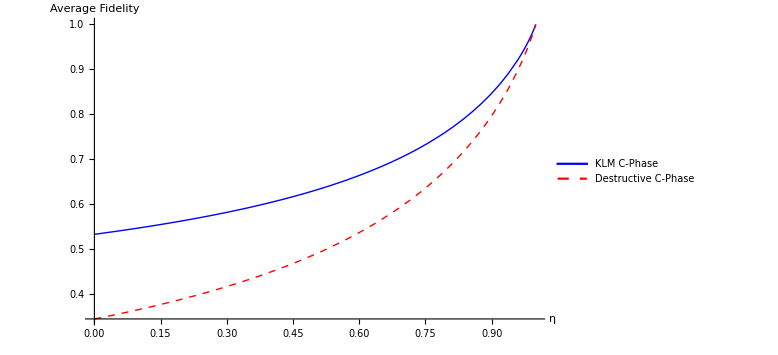

```mathematica
Plot[{AvFKLM[η],AvF[η]},{η,0,1},PlotRange->Full,LabelStyle->Large,AxesLabel->{"η","Average Fidelity"},ImageSize->Large,RotateLabel->True,PlotLegends->Placed[{"KLM C-Phase","Destructive C-Phase"},{0.35,.75}],PlotStyle->{{Thick,Blue},{Thick,Dashed,Red}},AxesStyle->{{Thick,Black},{Thick,Black}}]
```